```mathematica
NALOGA 1
```

```mathematica
d = Daljica[{-1, 1}, {3, -1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB - AA]
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_, BB_]] := Line[{AA, BB}]
Slika[d]
```

Line[{{-1,1},{3,-1}}]

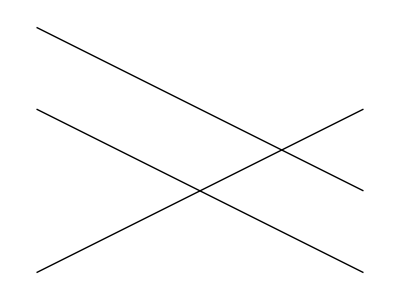

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_, BB_]] := 
Module[{x1, y1, x2, y2, k, n},
{x1, y1} = AA;
{x2, y2} = BB;
k = (y2 - y1)/(x2 - x1);
n = n /.First[Solve[y1 == k * x1 + n, n]];
y == k*x + n
]
EnacbaNosilke[d]
```

y==1/2-x/2

```mathematica
NALOGA 2
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]

Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

```mathematica
{}
ClearAll[x, y]
```

```mathematica
NALOGA 3
```

```mathematica
ClearAll[Slika]
```

```mathematica
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]] := Line[{{0, 0}, {1, 1}, {0, 3}, {-1, 2}}]
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

```mathematica
Narisi[m1_] := Graphisc[Slika[m1]]
Narisi[m1]
```

-Graphics-

```mathematica
PravilniNKotnik[n_, r_] := Graphics[{Line[Table[{r * cos[(2Pi * i)/n]}, {i, 0, n}]]}]
PravilniNKotnik[5, 2]
```

-Graphics-

```mathematica
PravilniNKotnik[n_, r_, phi_] := Graphics[{Line[Table[{r*cos[(2Pi * i + phi)/n], r *Sin[(2Pi*i + phi)/n]},  {i, 0, n}]], Point[{0, 0}]}]
Manipulate[PravilniNKotnik[5, 2, phi], {phi, 1.57, 33}]
```

```mathematica
NALOGA 5
```

```mathematica
VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]
VsiPari[f, {1, 2, 3}, {a, b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]
VsiPari[{1, 2, 3}, {2, 8, 6}, {4, 5}]
```

{{1,2,3}[2,4],{1,2,3}[2,5],{1,2,3}[8,4],{1,2,3}[8,5],{1,2,3}[6,4],{1,2,3}[6,5]}

```mathematica
z = List[{1, 2, 3}, {2, 8, 6}, {4, 5}]
```

{{1,2,3},{2,8,6},{4,5}}

```mathematica
p3 = Flatten[z]
```

{1,2,3,2,8,6,4,5}

```mathematica
p4 = Outer[f, z,z]
```

{{{{f[1,1],f[1,2],f[1,3]},{f[1,2],f[1,8],f[1,6]},{f[1,4],f[1,5]}},{{f[2,1],f[2,2],f[2,3]},{f[2,2],f[2,8],f[2,6]},{f[2,4],f[2,5]}},{{f[3,1],f[3,2],f[3,3]},{f[3,2],f[3,8],f[3,6]},{f[3,4],f[3,5]}}},{{{f[2,1],f[2,2],f[2,3]},{f[2,2],f[2,8],f[2,6]},{f[2,4],f[2,5]}},{{f[8,1],f[8,2],f[8,3]},{f[8,2],f[8,8],f[8,6]},{f[8,4],f[8,5]}},{{f[6,1],f[6,2],f[6,3]},{f[6,2],f[6,8],f[6,6]},{f[6,4],f[6,5]}}},{{{f[4,1],f[4,2],f[4,3]},{f[4,2],f[4,8],f[4,6]},{f[4,4],f[4,5]}},{{f[5,1],f[5,2],f[5,3]},{f[5,2],f[5,8],f[5,6]},{f[5,4],f[5,5]}}}}

```mathematica
m2 = RegularPolygon[1, 4]
```

RegularPolygon[1,4]

```mathematica
NALOGA 6
```

```mathematica
Imamo vektorja x in y tako, da velja |x| = 3 in |y| = 4. Določi dolžino vektroja 9y - 2x.
```

```mathematica
ClearAll[x, y]
```

```mathematica
Dana sta vektorja x = 3 in y = 4, ki oklepata kot Pi/3.
```

```mathematica
x = 3
y = 4
```

```mathematica
xy == 3*4*Cos[Pi/3]
```

xy==6

```mathematica
Solve[81*y^2 - 36*6 +4*x^2]
```

Solve::naqs: 1116 is not a quantified system of equations and inequalities.

Solve[1116]

```mathematica
Dolžina vektorja 9y - 2x je 1116 enot.
```